# Report Project 1

Course code: IX1500
Date: 2017-09-13

Evan Saboo, name1@kth.se
Xing Guan, xguan@kth.se

Task 1a: Poker Probability by census method

## Summery

### Task

The first task is to calculate the exact probability of the following hands in a variation of a poker game:

one pair

two pairs

three of a kind

four of a kind

five of a kind

full hand

straight

flush

straight flush

nothing

To calculate the exact probability  we will be using the census method.
The poker game consists of the cards 8,9,10,J,Q,K,A from two decks to construct sets of five playing cards. If one of the hand does contain more than one rank then the highest rank is considered e.g. if we want to calculate the probability of three of a kind and one of hands contains one pair, two pairs, three of a kind and full hand then the highest rank (full hand) is considered and it will be excluded from the calculation.

### Result

Hand | Probability | Probability,%
One pair | 11920/22737 | 0,5242556186
Two pair | 870/7579 | 0,1147908695
Three of a kind | 2240/22737 | 0,09851783437
Four of a kind | 140/22737 | 0,006157364648
Five of a kind | 7/68211 | 0,0001026227441
Full hand | 392/22737 | 0,01724062101
Straight | 1360/53053 | 0,02563474262
Flush | 953/477477 | 0,001995907656
Straight flush | 16/159159 | 0,0001005284024
Nothing | 0 | □

## Calculating poker Probability by census method

### A pair

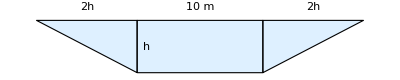

The given trapezoid area is

a(h)=(10+2h)h

0 | 0 | 0
200 | 2.6 | 39.52
400 | 5.1 | 103.02
600 | 6.3 | 142.38
800 | 4.3 | 79.98
1000 | 2.6 | 39.52
1200 | 1.3 | 16.38
1400 | 1.7 | 22.78
1600 | 2.8 | 43.68
1800 | 1.5 | 19.5
2000 | 0 | 0

The data is interpolated as a function A(x).

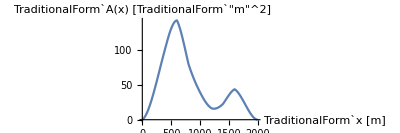

### Two pairs

The requested volume to be transported can be calculated numerically with the integral

V=∫_0^2000 A(x)dx

V≈101×10^3 m^3

I.e. about 0.1 km^3 must be transported.

## Code

Task 1b: Poker Probability by combinatorial calculus

## Summery

### Task

The second task is to use combinatorial calculus to calculate the probability of flush, straight, full house, 3 of a kind and 4 of a kind. Every rank has to be compared to task 1a to check if the answers match.

### Result

The results is calculated by using combinatorial calculus which is also confirmed with the answer from task 1a.

Hand | Probability | Probability,%
Flush | 953/477477 | 0.1995907656
Straight | 1360/53053 | 2.563474262
Full house | 392/22737 | 1.724062101
3 of a kind | 2240/22737 | 9.851783437
4 of a kind | 140/22737 | 0.6157364648

## Using combinatorial calculus method to estimate the probability in Poker

### Flush

First we choose 5 cards from 14 cards with same color, there are 7 cards with same color in one deck ranging from 8 to A, with 2 decks we got 14 cards with same color. We have to choose 1 of 4 different colors. Finally we have to excluding the straight flush, where it has 3 possible straight from 8 cards ranging from 8 to A. The multiplication principle gives the result.
n_(different color)=Binomial[4, 1],n_(5cards)=Binomial[14, 5], n_(straight each color)=Binomial[3, 1], n_(1 card)=Binomial[8, 1]
n_(flush(incl. straight flush))=n_(different color)n_(5cards)=Binomial[4, 1] Binomial[14, 5]
Because there are 2 set of 4 different color which give a combination of square of 4 which is 16.
n_(straight flush)=n_(straight each color)n_(1card)=16Binomial[3, 1] Binomial[8, 1]
∴P_flush=(n_(flush -)n_(straight flush))/n_tot=(Binomial[4, 1] Binomial[14, 5]-16Binomial[3, 1] Binomial[8, 1])/Binomial[56, 5]=953/477477≈0.1995907656%

### Straight

There are 3 different ways to create straight for each deck of same color ranging from 8 to A. From the two sets of deck we can choose 1 of 8 cards, and we have to choose that 5 times. Due to the multiplication principle, it gives us 8 choose 1 elevated with 5. In the end we need to excluding the straight flush which is included in straight.

 n_(straight each color)=Binomial[3, 1], n_(one card of each value)=Binomial[8, 1]
n_straight=n_(straight each color),n_(one card of each value ^5)=Binomial[3, 1] Binomial[8, 1]^5
Just as mentioned before the straight flush need to be subtracted.
n_(straight flush)=n_(straight each color)n_(1card)=16Binomial[3, 1] Binomial[8, 1]
∴P_straight=n_straight/n_tot=(Binomial[3, 1] Binomial[8, 1]^5 -16 Binomial[3, 1]Binomial[8, 1])/Binomial[56, 5]=1360/53053≈2.56347426%

### Full house

First we choose one of seven possibilities to be kind value x, then we choose three out of the eight x. And same with the one pair value y, we choose one of six possibilities which is left after have choose three card of x. The multiplication principle gives the result.
 n_(one of seven cards)=Binomial[7, 1], n_(three card of same value)=Binomial[8, 3],  n_(one of six)=Binomial[6, 1], n_(two card of each value)=Binomial[8, 2]
n_(full house)=n_(one of seven cards)n_(three card of same value)n_(one of six)n_(two card of each value)=Binomial[7, 1]Binomial[8, 3]Binomial[6, 1] Binomial[8, 2]
∴P_(full house)=(n_(full house))/n_tot=(Binomial[7, 1] Binomial[8, 3] Binomial[6, 1]Binomial[8, 2])/Binomial[56, 5]=392/22737≈1.724062101%

### 3 of a kind

In order to find 3 kind, we choose one of seven possibilities of value x, we take three cards out of eight. Then we can just take randomly 2 cards out of 48 cards without value x. Secondly we need to subtract full house to get the right answer.
 n_(one of seven cards)=Binomial[7, 1], n_(three card of same value)=Binomial[8, 3],  n_(2 out of 48)=Binomial[48, 2]
n_(three kind)=n_(one of seven cards)n_(three card of same value)n_(2 out of 48)=Binomial[7, 1]Binomial[8, 3]Binomial[48, 2] 
∴P_(three kind)=(n_(three kind))/n_tot=(Binomial[7, 1] Binomial[8, 3] Binomial[48, 2] - full house(taking the value from earlier))/Binomial[56, 5]=2240/22737≈9.851783437%

### 4 of a kind

To calculate four kind we take one of seven possibilities and we can choose four of eight cards with same value. There are one card that we can choose out of 48 cards.
n_value=Binomial[7, 1],n_(4cards)=Binomial[8, 4], n_last=Binomial[48, 1]
n_4=n_value n_(4cards)n_last=Binomial[7, 1] Binomial[8, 4]Binomial[48, 1]
∴P_4=n_4/n_tot=(Binomial[7, 1] Binomial[8, 4]Binomial[48, 1])/Binomial[56, 5]=23520/3819816=140/22737≈0.615736%

## Code

```mathematica
ClearAll["`*"]
```

Flush

```mathematica
Flush = (Binomial[14,5]*Binomial[4,1]-Binomial[3,1]*Binomial[8,1]*16)/Binomial[56,5]
```

953/477477

Straight

```mathematica
straight = (Binomial[3,1]*Binomial[8,1]^5-Binomial[3,1]*Binomial[8,1]*16)/Binomial[56,5]
```

1360/53053

Full house

```mathematica
fullHouse= Binomial[7,1]*Binomial[8,3]*Binomial[6,1]*Binomial[8,2]/Binomial[56,5]
```

392/22737

3 of a kind

```mathematica
threeKind = (Binomial[7,1]*Binomial[8,3]*Binomial[48,2]/Binomial[56,5]) - fullHouse
```

2240/22737

4 of a kind

```mathematica
fourKind = Binomial[7,1]*Binomial[8,4]*Binomial[48,1]/Binomial[56,5]
```

140/22737

Task 1c: Poker Probability by Monte Carlo method

## Summery

### Task

In this task we are going to calculate the probability of getting one pair using the Monte Carlo method. We will also draw a diagram that shows how the probability estimate stabilises with increasing sample size. This task will also be compared to task 1a to check if our approximate answer is close to the exact answer.

### Result

Using Monte Carlo method to estimate the probability of getting one pair after 3000 games. We came up with a probability of 53.133 % after 3000 hands/games. Each game is defined as one hand with 5 cards each hand. The result from estimation of Monte Carlo can compare with the result from task 1 which is 52.426 %.

## Calculating probability of one pair using Monte Carlo

### Solution to calculate one pair

We start with randomly choosing 5 cards from the decks which represent as a randomly hand.
Secondly we work numerically starting by multiplying the randomly hand with 100 up to 3000 times, which represent the amount of hand. For each hand which is a pair will count as true and false otherwise using the code from task 1. And for every true is counted as 1 and false 0. 

We count all the trues and dividing it by the amount of hands we created which gives the probability of one pair using Monte Carlo. We can observe that the result is varying a lot ranging 1 to 500 hands/games. The result quickly stabilize and converge after 500 games and even more after 1000 games that as we can see in the diagram below.

Games,# | Probability,%
100 | 57
200 | 53.212
300 | 53
400
500
600
700
800
900
1000
1500
2000
2500
3000 | 49.752
48.8
56.333
50.571
50
55.223
51.721
52.273
52
51.447
53.133

The table above demonstration the probability with the responding amount of games.

The amount of games is determined to be 3000 games in this case.The reason is that in the diagram below,we can see the probability begin to converge after a few hundred of games and the line is varying much less after 2000 games comparing to the beginning. The principle is that with more data,the method gives more confidence in it's result.

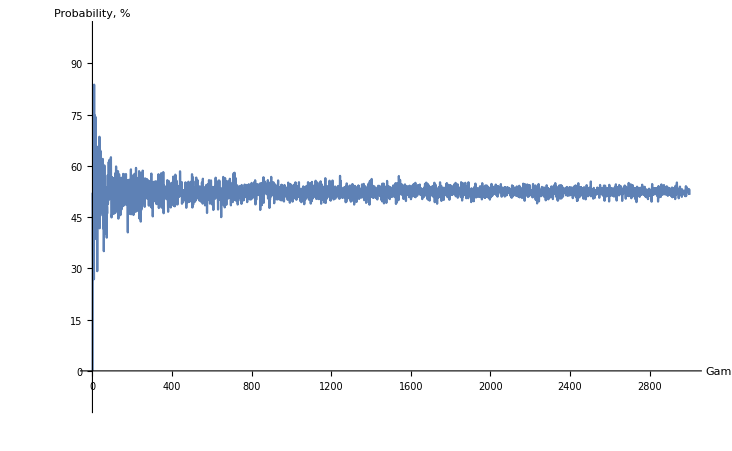

The diagram above illustrate the probability of getting one pair using Monte Carlo method with increasing games/hands.

## Code

We are using the deck and randomly select 5 cards which represent a play or a hand.

```mathematica
Clear[play]
play := Sort/@Partition[RandomSample[deck, 1*5], 5]
```

Create the function omega3 where the parameter is used to multiply the play

```mathematica
Clear[omega3]
omega3[n_] := Table[play, {n}];
```

Example, creating a table with n = 2000, which says the function creates 2000 plays or hands.

```mathematica
n = 2000;
omega3[n_] := Table[play, {n}];  
omega3[n]
```

Function p3 is calculating the probability of one pair from random selected hands.

```mathematica
Clear[pair3]
pair3[play_] := Or@@pairQs/@play
Clear[p3]
p3[n_] := (Count[omega3[n], _?(pair3)]*100)/(n);
```

Plot is used in order to create a diagram which illustrates the probability with increasing games/hands.

```mathematica
Plot[p3[n],{n,1,3000}, AxesLabel->{"Game", "Probability, %"}, PlotRange->{-0.1*100,1*100}]
```